```mathematica
ZeVars8=Table[allGraphs5[k,"colofour"],{k,Select[allGraphs5AtomKeys,allGraphs5[#,"comp"]===GreaterEqual& ]}]
```

{v1x2x3x45,v1x2x35x4,v1x2x34x5,v1x25x3x4,v1x25x34,v1x24x3x5,v1x24x35,v1x245x3,v1x23x4x5,v1x235x4,v15x2x3x4,v15x24x3,v14x2x3x5,v14x2x35,v14x25x3,v14x23x5,v14x235,v13x2x4x5,v13x2x45,v13x25x4,v13x24x5,v13x245,v135x2x4,v135x24,v134x2x5,v134x25,v12x3x4x5,v12x35x4,v124x3x5,v124x35}

```mathematica
Length[ZeVars8]
```

30

```mathematica
Table[allGraphs5[k,"comp"],{k,allGraphs5AtomKeys}]//Tally
```

{{Equal,1},{GreaterEqual,30},{Greater,21}}

```mathematica
ZeVars8//Length
```

30

```mathematica
allCrit=Map[Sort,BooleanMinimize[Reduce[
With[
{base="C",colofour="colofour"},
Fold[And,
Map[Fold[Or,Table[var>(var/.RepAtLeast[base]),{var,ListofVars[(allGraphs5[#,colofour]/.RepZero[base])]}]]&,
Select[Keys[allGraphs5],(allGraphs5[#,"atleast"]≠ (allGraphs5[#,colofour]/.RepAtLeast[base]))&]
]
]
]
]]];
```

```mathematica
tri=Table[allGraphs5[k,"colofour"],{k,alfa1s}];
```

```mathematica
allCrit2=Map[ListofVars,ExpressionToList[allCrit]];Length[allCrit2]/32
```

17

```mathematica
allCrit3=Select[Map[ListofVars,ExpressionToList[allCrit]],Intersection[#,tri]=={}&];Length[allCrit3]
```

32

```mathematica
Take[allCrit3,3]
```

{{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x23x5,v14x2x3x5,v15x2x3x4,v1x235x4,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45},{v124x35,v12x3x4x5,v134x25,v135x24,v13x2x45,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x245x3,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4}}

```mathematica
BaseCoeff2[formula__,base_]:=Table[Coefficient[formula,var],{var,Bases[base,"Variables"]}]
```

```mathematica
Total[{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45}]
```

v124x35+v12x3x4x5+v134x25+v135x24+v13x245+v13x2x4x5+v14x235+v14x2x3x5+v15x2x3x4+v1x23x4x5+v1x24x3x5+v1x25x3x4+v1x2x34x5+v1x2x35x4+v1x2x3x45

```mathematica
BaseCoeff2[Total[{v124x35,v12x3x4x5,v134x25,v135x24,v13x245,v13x2x4x5,v14x235,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45}],"C"]
```

{0,1,1,1,1,1,1,1,1,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,1,0,0,0}

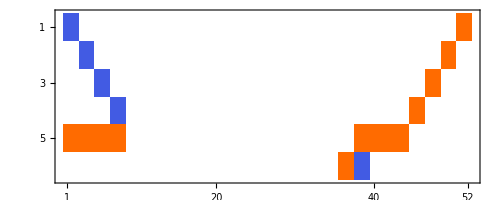

```mathematica
Map[BaseCoeff2[Total[#],"C"]&,allCrit3]//LatticeReduce//Sort//Transpose//Sort//Transpose//MatrixPlot
```

```mathematica
Clear[Buddy]
```

```mathematica
Buddy[master_,cond_:allCrit3]:=Select[ZeVars8,With[{slave=#},
With[{masterClass=Select[cond,MemberQ[#,master]&]},SymbolName[master]=!=SymbolName[slave]&&Length[masterClass]≠0&&Length[Select[masterClass,MemberQ[#,slave]&]]==Length[masterClass]==Length[Select[cond,MemberQ[#,slave]&]]
]
]&]
```

```mathematica
Table[master->Buddy[master],{master,ZeVars8}]/.RepGraph["C"]
```

{-Graphics-295250→{-Graphics-361940},-Graphics-295270→{-Graphics-295510,-Graphics-296050,-Graphics-317110,-Graphics-360850},-Graphics-295330→{-Graphics-383080},-Graphics-295510→{-Graphics-295270,-Graphics-296050,-Graphics-317110,-Graphics-360850},-Graphics-295600→{-Graphics-382810},-Graphics-296050→{-Graphics-295270,-Graphics-295510,-Graphics-317110,-Graphics-360850},-Graphics-296080→{},-Graphics-296330→{-Graphics-360860},-Graphics-297670→{-Graphics-319840},-Graphics-297970→{-Graphics-319540},-Graphics-302530→{-Graphics-368980},-Graphics-303340→{-Graphics-368170},-Graphics-317110→{-Graphics-295270,-Graphics-295510,-Graphics-296050,-Graphics-360850},-Graphics-317140→{},-Graphics-317380→{},-Graphics-319540→{-Graphics-297970},-Graphics-319840→{-Graphics-297670},-Graphics-360850→{-Graphics-295270,-Graphics-295510,-Graphics-296050,-Graphics-317110},-Graphics-360860→{-Graphics-296330},-Graphics-361120→{},-Graphics-361660→{},-Graphics-361940→{-Graphics-295250},-Graphics-368170→{-Graphics-303340},-Graphics-368980→{-Graphics-302530},-Graphics-382810→{-Graphics-295600},-Graphics-383080→{-Graphics-295330},-Graphics-492070→{-Graphics-514780},-Graphics-492100→{-Graphics-514750},-Graphics-514750→{-Graphics-492100},-Graphics-514780→{-Graphics-492070}}

```mathematica
AntiBuddy[master_,cond_:allCrit3]:=Select[ZeVars8,With[{slave=#},
With[{masterClass=Select[cond,MemberQ[#,master]&]},
Length[masterClass]≠0&&Length[Select[masterClass,!MemberQ[#,slave]&]]==Length[masterClass]==Length[Select[cond,MemberQ[#,slave]&]]
]
]&]
```

```mathematica
Table[master->AntiBuddy[master],{master,ZeVars8}]/.RepGraph["C"]
```

{-Graphics-295250→{-Graphics-296330,-Graphics-360860},-Graphics-295270→{},-Graphics-295330→{-Graphics-295600,-Graphics-382810},-Graphics-295510→{},-Graphics-295600→{-Graphics-295330,-Graphics-383080},-Graphics-296050→{},-Graphics-296080→{},-Graphics-296330→{-Graphics-295250,-Graphics-361940},-Graphics-297670→{-Graphics-297970,-Graphics-319540},-Graphics-297970→{-Graphics-297670,-Graphics-319840},-Graphics-302530→{-Graphics-303340,-Graphics-368170},-Graphics-303340→{-Graphics-302530,-Graphics-368980},-Graphics-317110→{},-Graphics-317140→{},-Graphics-317380→{},-Graphics-319540→{-Graphics-297670,-Graphics-319840},-Graphics-319840→{-Graphics-297970,-Graphics-319540},-Graphics-360850→{},-Graphics-360860→{-Graphics-295250,-Graphics-361940},-Graphics-361120→{},-Graphics-361660→{},-Graphics-361940→{-Graphics-296330,-Graphics-360860},-Graphics-368170→{-Graphics-302530,-Graphics-368980},-Graphics-368980→{-Graphics-303340,-Graphics-368170},-Graphics-382810→{-Graphics-295330,-Graphics-383080},-Graphics-383080→{-Graphics-295600,-Graphics-382810},-Graphics-492070→{-Graphics-492100,-Graphics-514750},-Graphics-492100→{-Graphics-492070,-Graphics-514780},-Graphics-514750→{-Graphics-492070,-Graphics-514780},-Graphics-514780→{-Graphics-492100,-Graphics-514750}}

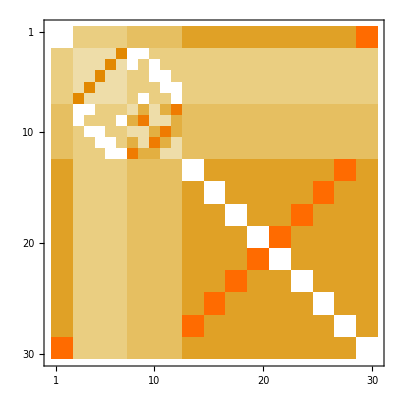

```mathematica
Sort[Transpose[Sort[Transpose[Table[
Table[
Select[Map[ListofVars,ExpressionToList[allCrit]],MemberQ[#,master]&&MemberQ[#,slave]&]//Length
,{slave,ZeVars8}
]
,{master,ZeVars8}]//Sort]]]]//MatrixPlot
```

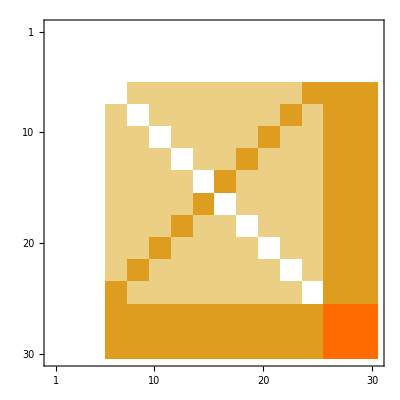

```mathematica
Transpose[Sort[Transpose[Table[
Table[
Select[allCrit3,MemberQ[#,master]&&MemberQ[#,slave]&]//Length
,{slave,ZeVars8}
]
,{master,ZeVars8}]//Sort]]]//MatrixPlot
```

```mathematica
allCrit4=Select[Map[ListofVars,ExpressionToList[allCrit]],Length[Intersection[#,tri]]==5&];Length[allCrit4]
```

32

```mathematica
Table[master->AntiBuddy[master,allCrit4],{master,ZeVars8}]/.RepGraph["C"]//Multicolumn
```

-Graphics-295250→{-Graphics-296330,-Graphics-360860} | -Graphics-296050→{} | -Graphics-302530→{-Graphics-303340,-Graphics-368170} | -Graphics-319540→{-Graphics-297670,-Graphics-319840} | -Graphics-361660→{} | -Graphics-383080→{-Graphics-295600,-Graphics-382810}
-Graphics-295270→{} | -Graphics-296080→{} | -Graphics-303340→{-Graphics-302530,-Graphics-368980} | -Graphics-319840→{-Graphics-297970,-Graphics-319540} | -Graphics-361940→{-Graphics-296330,-Graphics-360860} | -Graphics-492070→{-Graphics-492100,-Graphics-514750}
-Graphics-295330→{-Graphics-295600,-Graphics-382810} | -Graphics-296330→{-Graphics-295250,-Graphics-361940} | -Graphics-317110→{} | -Graphics-360850→{} | -Graphics-368170→{-Graphics-302530,-Graphics-368980} | -Graphics-492100→{-Graphics-492070,-Graphics-514780}
-Graphics-295510→{} | -Graphics-297670→{-Graphics-297970,-Graphics-319540} | -Graphics-317140→{} | -Graphics-360860→{-Graphics-295250,-Graphics-361940} | -Graphics-368980→{-Graphics-303340,-Graphics-368170} | -Graphics-514750→{-Graphics-492070,-Graphics-514780}
-Graphics-295600→{-Graphics-295330,-Graphics-383080} | -Graphics-297970→{-Graphics-297670,-Graphics-319840} | -Graphics-317380→{} | -Graphics-361120→{} | -Graphics-382810→{-Graphics-295330,-Graphics-383080} | -Graphics-514780→{-Graphics-492100,-Graphics-514750}

```mathematica
Table[master->Buddy[master,allCrit4],{master,ZeVars8}]/.RepGraph["C"]
```

{-Graphics-295250→{-Graphics-361940},-Graphics-295270→{},-Graphics-295330→{-Graphics-383080},-Graphics-295510→{},-Graphics-295600→{-Graphics-382810},-Graphics-296050→{},-Graphics-296080→{-Graphics-317140,-Graphics-317380,-Graphics-361120,-Graphics-361660},-Graphics-296330→{-Graphics-360860},-Graphics-297670→{-Graphics-319840},-Graphics-297970→{-Graphics-319540},-Graphics-302530→{-Graphics-368980},-Graphics-303340→{-Graphics-368170},-Graphics-317110→{},-Graphics-317140→{-Graphics-296080,-Graphics-317380,-Graphics-361120,-Graphics-361660},-Graphics-317380→{-Graphics-296080,-Graphics-317140,-Graphics-361120,-Graphics-361660},-Graphics-319540→{-Graphics-297970},-Graphics-319840→{-Graphics-297670},-Graphics-360850→{},-Graphics-360860→{-Graphics-296330},-Graphics-361120→{-Graphics-296080,-Graphics-317140,-Graphics-317380,-Graphics-361660},-Graphics-361660→{-Graphics-296080,-Graphics-317140,-Graphics-317380,-Graphics-361120},-Graphics-361940→{-Graphics-295250},-Graphics-368170→{-Graphics-303340},-Graphics-368980→{-Graphics-302530},-Graphics-382810→{-Graphics-295600},-Graphics-383080→{-Graphics-295330},-Graphics-492070→{-Graphics-514780},-Graphics-492100→{-Graphics-514750},-Graphics-514750→{-Graphics-492100},-Graphics-514780→{-Graphics-492070}}

```mathematica
Table[master->Buddy[master,Map[ListofVars,ExpressionToList[allCrit]]],{master,ZeVars8}]/.RepGraph["C"]
```

{-Graphics-295250→{-Graphics-361940},-Graphics-295270→{},-Graphics-295330→{-Graphics-383080},-Graphics-295510→{},-Graphics-295600→{-Graphics-382810},-Graphics-296050→{},-Graphics-296080→{},-Graphics-296330→{-Graphics-360860},-Graphics-297670→{-Graphics-319840},-Graphics-297970→{-Graphics-319540},-Graphics-302530→{-Graphics-368980},-Graphics-303340→{-Graphics-368170},-Graphics-317110→{},-Graphics-317140→{},-Graphics-317380→{},-Graphics-319540→{-Graphics-297970},-Graphics-319840→{-Graphics-297670},-Graphics-360850→{},-Graphics-360860→{-Graphics-296330},-Graphics-361120→{},-Graphics-361660→{},-Graphics-361940→{-Graphics-295250},-Graphics-368170→{-Graphics-303340},-Graphics-368980→{-Graphics-302530},-Graphics-382810→{-Graphics-295600},-Graphics-383080→{-Graphics-295330},-Graphics-492070→{-Graphics-514780},-Graphics-492100→{-Graphics-514750},-Graphics-514750→{-Graphics-492100},-Graphics-514780→{-Graphics-492070}}

```mathematica
Table[master->AntiBuddy[master,Map[ListofVars,ExpressionToList[allCrit]]],{master,ZeVars8}]/.repFullEmbed
```

{10→{10,8},6→{},20→{31,7},11→{},31→{20,9},6→{},0→{},10→{10,4},10→{10,8},10→{10,4},11→{8,13},8→{11,5},9→{},3→{},8→{},8→{10,4},4→{10,8},9→{},8→{10,4},8→{},3→{},4→{10,8},13→{11,5},5→{8,13},7→{20,9},9→{31,7},11→{8,13},8→{11,5},13→{11,5},5→{8,13}}

```mathematica
Table[(master/.RepAtLeast["C"]),{master,ZeVars8}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
allGraphs5[0,"atleast"]
```

34

```mathematica
Clear[RepGraph2];RepGraph2[base_]:=RepGraph2[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->Labeled[ShowGraph5Least[key],Rotate[Style[SymbolToLabel2[allGraphs5[key,Bases[base,"Colofour"]]],Red],Pi/2],Left],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Sort[Table[master->Buddy[master,Map[ListofVars,ExpressionToList[allCrit]]],{master,ZeVars8}]/.RepGraph2["C"]]//TableForm
```

-Graphics-514780124♁35→{-Graphics-49207012}
-Graphics-31984014♁235→{-Graphics-29767023}
-Graphics-368980135♁24→{-Graphics-30253015}
-Graphics-36194013♁245→{-Graphics-29525045}
-Graphics-383080134♁25→{-Graphics-29533034}
-Graphics-514750124→{-Graphics-49210012♁35}
-Graphics-49210012♁35→{-Graphics-514750124}
-Graphics-382810134→{-Graphics-29560025♁34}
-Graphics-31954014♁23→{-Graphics-297970235}
-Graphics-36166013♁24→{}
-Graphics-368170135→{-Graphics-30334015♁24}
-Graphics-297970235→{-Graphics-31954014♁23}
-Graphics-36112013♁25→{}
-Graphics-36086013♁45→{-Graphics-296330245}
-Graphics-30334015♁24→{-Graphics-368170135}
-Graphics-296330245→{-Graphics-36086013♁45}
-Graphics-31738014♁25→{}
-Graphics-29560025♁34→{-Graphics-382810134}
-Graphics-31714014♁35→{}
-Graphics-29608024♁35→{}
-Graphics-49207012→{-Graphics-514780124♁35}
-Graphics-36085013→{}
-Graphics-29767023→{-Graphics-31984014♁235}
-Graphics-31711014→{}
-Graphics-29605024→{}
-Graphics-29533034→{-Graphics-383080134♁25}
-Graphics-30253015→{-Graphics-368980135♁24}
-Graphics-29551025→{}
-Graphics-29525045→{-Graphics-36194013♁245}
-Graphics-29527035→{}

```mathematica
Sort[Table[master->AntiBuddy[master,Map[ListofVars,ExpressionToList[allCrit]]],{master,ZeVars8}]/.RepGraph2["C"]]//TableForm
```

-Graphics-514780124♁35→{-Graphics-49210012♁35,-Graphics-514750124}
-Graphics-31984014♁235→{-Graphics-297970235,-Graphics-31954014♁23}
-Graphics-368980135♁24→{-Graphics-30334015♁24,-Graphics-368170135}
-Graphics-36194013♁245→{-Graphics-296330245,-Graphics-36086013♁45}
-Graphics-383080134♁25→{-Graphics-29560025♁34,-Graphics-382810134}
-Graphics-514750124→{-Graphics-49207012,-Graphics-514780124♁35}
-Graphics-49210012♁35→{-Graphics-49207012,-Graphics-514780124♁35}
-Graphics-382810134→{-Graphics-29533034,-Graphics-383080134♁25}
-Graphics-31954014♁23→{-Graphics-29767023,-Graphics-31984014♁235}
-Graphics-36166013♁24→{}
-Graphics-368170135→{-Graphics-30253015,-Graphics-368980135♁24}
-Graphics-297970235→{-Graphics-29767023,-Graphics-31984014♁235}
-Graphics-36112013♁25→{}
-Graphics-36086013♁45→{-Graphics-29525045,-Graphics-36194013♁245}
-Graphics-30334015♁24→{-Graphics-30253015,-Graphics-368980135♁24}
-Graphics-296330245→{-Graphics-29525045,-Graphics-36194013♁245}
-Graphics-31738014♁25→{}
-Graphics-29560025♁34→{-Graphics-29533034,-Graphics-383080134♁25}
-Graphics-31714014♁35→{}
-Graphics-29608024♁35→{}
-Graphics-49207012→{-Graphics-49210012♁35,-Graphics-514750124}
-Graphics-36085013→{}
-Graphics-29767023→{-Graphics-297970235,-Graphics-31954014♁23}
-Graphics-31711014→{}
-Graphics-29605024→{}
-Graphics-29533034→{-Graphics-29560025♁34,-Graphics-382810134}
-Graphics-30253015→{-Graphics-30334015♁24,-Graphics-368170135}
-Graphics-29551025→{}
-Graphics-29525045→{-Graphics-296330245,-Graphics-36086013♁45}
-Graphics-29527035→{}

```mathematica
Sort[Table[master->Buddy[master,Map[ListofVars,ExpressionToList[allCrit]]]->(master/.RepAtLeast["C"]),{master,ZeVars8}]/.repFullEmbed]//TableForm
```

0→{}→0
3→{}→0
3→{}→0
4→{10}→0
4→{10}→0
5→{11}→0
5→{11}→0
6→{}→0
6→{}→0
7→{31}→0
8→{}→0
8→{}→0
8→{10}→0
8→{10}→0
8→{13}→0
8→{13}→0
9→{}→0
9→{}→0
9→{20}→0
10→{4}→0
10→{4}→0
10→{8}→0
10→{8}→0
11→{}→0
11→{5}→0
11→{5}→0
13→{8}→0
13→{8}→0
20→{9}→0
31→{7}→0

```mathematica
Sort[Table[master->Buddy[master,Map[ListofVars,ExpressionToList[allCrit]]],{master,ZeVars8}]/.RepGraph2["C"]]//TableForm
```

```mathematica
Map[Grid[#,Frame->All]&,Block[{todo=Sort[ZeVars8,CompareSymbols],result={},current, buddy, anti,new},
While[todo≠{},
current=First[todo];
todo=Rest[todo];
buddy = Buddy[current];
anti=AntiBuddy[current];
new={Append[buddy,current],anti};
result=Append[result,new];
todo=Select[todo,!MemberQ[Flatten[new],#]&];
];
result
]/.RepGraph["C"]]
```

{-Graphics-514780 | -Graphics-492070
-Graphics-492100 | -Graphics-514750,-Graphics-295270 | -Graphics-295510 | -Graphics-296050 | -Graphics-317110 | -Graphics-360850
 |  |  |  | ,-Graphics-368980 | -Graphics-302530
-Graphics-303340 | -Graphics-368170,-Graphics-319840 | -Graphics-297670
-Graphics-297970 | -Graphics-319540,-Graphics-383080 | -Graphics-295330
-Graphics-295600 | -Graphics-382810,-Graphics-361940 | -Graphics-295250
-Graphics-296330 | -Graphics-360860,-Graphics-361660
,-Graphics-361120
,-Graphics-317380
,-Graphics-317140
,-Graphics-296080
}

```mathematica
GridBox[{{-Graphics-514780,-Graphics-492070},{-Graphics-492100,-Graphics-514750}}]
```

GridBox[{{-Graphics-514780,-Graphics-492070},{-Graphics-492100,-Graphics-514750}}]